# DK to Dp in SHARAQ04

```mathematica
c=299.792458;
m23F={21423.07758,9,23};
m22O={20498.06478,8,22};
m19N={17710.66578,7,19};
m16C={14914.53319,6,16};
m13B={12123.42998,5,13};
m10Be={9325.504152,4,10};
m7Li={6533.832577,3,7};
m8Li={7471.365332,3,8};
m4He={3727.379188,2,4};
m6He={5605.53449,2,6};
massList={m23F->"23F",m22O->"22O",m19N->"19N",m16C->"16C",m13B->"13B",m10Be->"10Be",m7Li->"7Li",m8Li->"8Li",m4He->"4He", m6He->"6He"};
Bρ = 6.7288; (* Tm *)
B0 = Bρ/4.4; (* T *)
xd = -1160.9; (* mm/100% *)
K0[m_]:=√(m[[1]]^2+c^2 m[[2]]^2 Bρ^2)-m[[1]];
KE[m_, x_]:=K0[m](1+x/xd);
p0[m_]:=c m[[2]] Bρ;
p[m_,K_]:=√((m[[1]]+K)^2-m[[1]]^2);
Dp[m_,K_]:=p[m,K]/p0[m]-1;
ρ[m_,K_]:=p[m,K]/(c m[[2]] B0);
Brho[m_,K_]:=ρ[m,K] B0;
β[m_,K_]:=p[m,K]/(m[[1]]+K);
```

```mathematica
Manipulate[
Plot[KE[mass,x], {x,-200,500}],
{{mass,m23F},massList}]
```

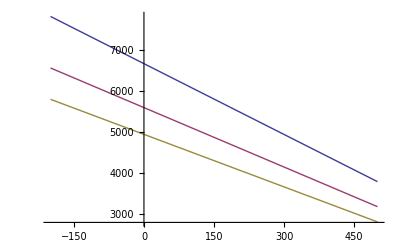

```mathematica
Plot[
Evaluate[Table[KE[mass,x],{mass, {m23F,m22O, m19N}}]],
 {x,-200,500}]
```

```mathematica
Table[p[mass,K0[mass]]/(mass[[2]] c),{mass, {m23F,m22O, m19N,m16C,m13B}}]
```

{6.7288,6.7288,6.7288,6.7288,6.7288}

```mathematica
Manipulate[Total[Table[(Dp[mass1,KE[mass1,x]]-Dp[mass2,KE[mass2,x]])^2, 
{x,-200,500,10}]/70],
{mass1, {m23F,m22O, m19N,m16C,m13B}},
{mass2, {m23F,m22O, m19N,m16C,m13B}}]
```

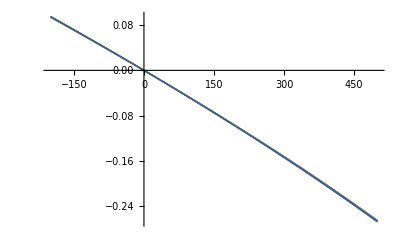

```mathematica
Plot[
Evaluate[Table[p[mass,KE[mass,x]]/mass[[2]]/(p[mass,K0[mass]]/mass[[2]])-1,{mass, {m23F,m22O, m19N,m16C,m13B}}]],
 {x,-200,500}]
```

```mathematica
Data=Table[{x,p[m23F,KE[m23F,x]]/p[m23F,K0[m23F]]-1},{x,-200,500,10}];
fit = Fit[Data,{x,x^2},x]
1/%[[2]]
Table[(p[m23F,KE[m23F,x]]/p[m23F,K0[m23F]]-1-fit/.{x->j})^2, {j,-200,500,10}]
```

-0.000488609 x-8.83431×10^-8 x^2

-(1.13195×10^7)/x^2

{1.00602×10^-6,8.01759×10^-7,6.31658×10^-7,4.91323×10^-7,3.76743×10^-7,2.84274×10^-7,2.10623×10^-7,1.52829×10^-7,1.08248×10^-7,7.45358×10^-8,4.96306×10^-8,3.1737×10^-8,1.93085×10^-8,1.10309×10^-8,5.80573×10^-9,2.73318×10^-9,1.09567×10^-9,3.41296×10^-10,6.74203×10^-11,4.48846×10^-12,0.,2.73484×10^-12,4.7249×10^-11,2.38686×10^-10,7.37945×10^-10,1.74727×10^-9,3.49626×10^-9,6.22847×10^-9,1.01885×10^-8,1.56099×10^-8,2.27034×10^-8,3.16465×10^-8,4.25737×10^-8,5.55672×10^-8,7.06497×10^-8,8.77774×10^-8,1.06835×10^-7,1.27632×10^-7,1.49901×10^-7,1.73294×10^-7,1.97388×10^-7,2.21687×10^-7,2.45626×10^-7,2.68581×10^-7,2.89881×10^-7,3.08818×10^-7,3.24666×10^-7,3.36705×10^-7,3.4424×10^-7,3.46633×10^-7,3.43335×10^-7,3.33926×10^-7,3.18155×10^-7,2.95994×10^-7,2.67695×10^-7,2.33847×10^-7,1.95454×10^-7,1.54011×10^-7,1.11597×10^-7,7.09685×10^-8,3.5676×10^-8,1.0183×10^-8,3.50579×10^-12,1.1853×10^-8,5.38148×10^-8,1.35525×10^-7,2.68377×10^-7,4.65746×10^-7,7.43237×10^-7,1.11896×10^-6,1.61384×10^-6}

```mathematica
Data=Table[{x,p[m23F,KE[m23F,x]]/9},{x,-200,500,10}];
fit = Fit[Data,{1,x,x^2},x]
Table[(p[m23F,KE[m23F,x]]/9-fit/.{x->j})^2, {j,-200,500,10}]
```

2018.03-0.985391 x-0.000184241 x^2

{2.33269,1.64926,1.11595,0.711482,0.416375,0.212917,0.0850711,0.018412,0.0000464554,0.0185409,0.0638462,0.127223,0.201166,0.279328,0.356449,0.428274,0.491482,0.543611,0.582984,0.60863,0.620218,0.617976,0.602626,0.575306,0.537507,0.490998,0.437762,0.379931,0.31972,0.259369,0.201081,0.146967,0.0989961,0.0589419,0.0283399,0.00844515,0.000196537,0.00418539,0.0206303,0.0493581,0.0897922,0.140948,0.201439,0.269486,0.342946,0.419346,0.495927,0.569707,0.637559,0.696297,0.742788,0.77408,0.787553,0.781085,0.753257,0.703572,0.632716,0.542838,0.437882,0.323947,0.209695,0.106803,0.0304743,5.7107×10^-9,0.0393853,0.178046,0.451579,0.902618,1.58178,2.54871,3.87323}

```mathematica
fit/.{x->0}
```

2018.03

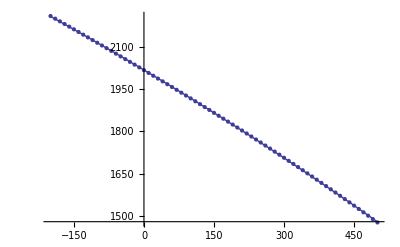

```mathematica
Show[
Plot[fit,{x,-200,500}],
ListPlot[Data]
]
```

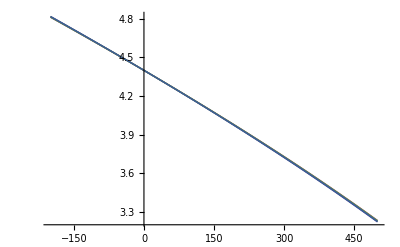

```mathematica
Plot[
Evaluate[Table[ρ[mass,KE[mass,x]],{mass, {m23F,m22O, m19N,m16C,m13B}}]],
 {x,-200,500}]
```

```mathematica
Data=Table[{x,ρ[m23F,KE[m23F,x]]},{x,-200,500,10}];
fit = Fit[Data,{1,x,x^2},x]
Table[(ρ[m23F,KE[m23F,x]]-fit/.{x->j})^2, {j,-200,500,10}]
```

4.40172-0.00214933 x-4.01865×10^-7 x^2

{0.000011098,7.84652×10^-6,5.30926×10^-6,3.38495×10^-6,1.98095×10^-6,1.01297×10^-6,4.04735×10^-7,8.7597×10^-8,2.21017×10^-10,8.82104×10^-8,3.03755×10^-7,6.05276×10^-7,9.57067×10^-7,1.32894×10^-6,1.69584×10^-6,2.03756×10^-6,2.33828×10^-6,2.58629×10^-6,2.77361×10^-6,2.89562×10^-6,2.95075×10^-6,2.94009×10^-6,2.86706×10^-6,2.73708×10^-6,2.55725×10^-6,2.33598×10^-6,2.0827×10^-6,1.80756×10^-6,1.5211×10^-6,1.23398×10^-6,9.56663×10^-7,6.99212×10^-7,4.70984×10^-7,2.80423×10^-7,1.3483×10^-7,4.01787×10^-8,9.35046×10^-10,1.99125×10^-8,9.81508×10^-8,2.34827×10^-7,4.27196×10^-7,6.70577×10^-7,9.58366×10^-7,1.28211×10^-6,1.6316×10^-6,1.99508×10^-6,2.35942×10^-6,2.71044×10^-6,3.03326×10^-6,3.31271×10^-6,3.53389×10^-6,3.68277×10^-6,3.74687×10^-6,3.7161×10^-6,3.5837×10^-6,3.34732×10^-6,3.01021×10^-6,2.58261×10^-6,2.08327×10^-6,1.54122×10^-6,9.97646×10^-7,5.08126×10^-7,1.44985×10^-7,2.71693×10^-14,1.8738×10^-7,8.47072×10^-7,2.14844×10^-6,4.2943×10^-6,7.52548×10^-6,0.0000121257,0.0000184273}

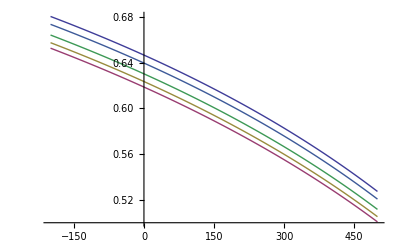

```mathematica
Plot[
Evaluate[Table[β[mass,KE[mass,x]],{mass, {m23F,m22O, m19N,m16C,m13B}}]],
 {x,-200,500}]
```

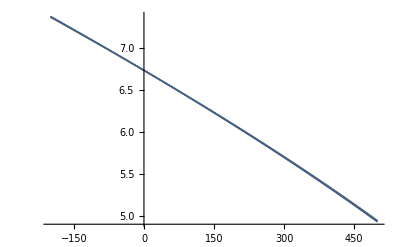

```mathematica
Plot[
Evaluate[Table[Brho[mass,KE[mass,x]],{mass, {m23F,m22O, m19N,m16C,m13B}}]],
 {x,-200,500}]
```